```mathematica
(*Aqui, vamos conduzir a evolução do plot do modelo STS usando a condição inicial do paper do muga mas sobre o Cp de Schrodinger daquela partícula, o mesmo que calculamos analíticamente no primeiro notebook*)
dndt[t_]:=NIntegrate[Abs[(E^((I*1*(0.5*(x+50)^2+2*1*t*(-50))-2*1*(1*t-2*0.5*x)*5^2)/(2*1*(1*t-2*I*0.5*5^2)))*(2*Pi)^(1/4)*(1*Sqrt[(I*1*t)/0.5+2*5^2]*Sqrt[(I*0.5*(1*(x+50)-2*I*1*5^2)^2)/(1^2*(1*t-2*I*0.5*5^2))]*Erf[Sqrt[(I*0.5*(1*x-1*(-50)-2*I*1*5^2)^2)/(1^2*(1*t-2*I*0.5*5^2))]/Sqrt[2]]+(1*(x+50)-2*I*1*5^2)*(-2*I+Erfi[(1*x-1*(-50)-2*I*1*5^2)/(1*Sqrt[(2*I*1*t)/0.5+4*5^2])])))/((5^2)^(1/4)*Sqrt[(2*I*1*t)/0.5+4*5^2]*((-I)*1*(x+50)-2*1*5^2))]^2*(2/(1*(x-1)*(x+(1/(1+I*1))))),{x,0.001,0.999}]
```

```mathematica
NIntegrate[Re[-dndt[t]], {t, 0, 60}]
```

1.15113

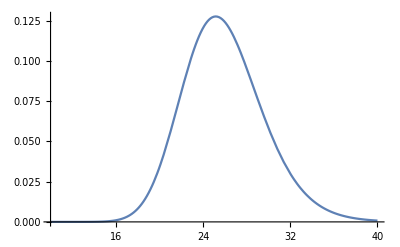

```mathematica
Plot[Re[-dndt[t]],{t,10,40},MaxRecursion->2]
```

```mathematica
dndtinterpol=FunctionInterpolation[Re[-dndt[t]],{t,10,60}]//Quiet
```

InterpolatingFunction[…]

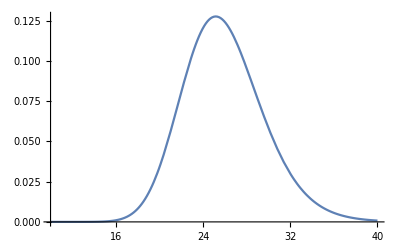

```mathematica
Plot[dndtinterpol[t],{t,10,40},MaxRecursion->2](*Plot da distribuição temporal do Muga dndt em x=0,tudo funcionando exatamente como no paper*)
```

```mathematica
(*atente aqui ao fato de que dndt ainda não foi normalizado; isto é*)
NIntegrate[dndtinterpol[t],{t, 10, 60}]
```

1.15113

```mathematica
NSolve[A*NIntegrate [dndtinterpol[t],{t,10,60}]==1,A](*Normalizando como fazemos normalmente*)
```

{{A→0.868708}}

```mathematica
dndtnorm[t_] := dndtinterpol[t]* 0.8687079633409152
```

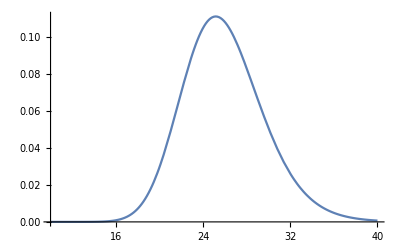

```mathematica
Plot[dndtnorm[t],{t,10,40},MaxRecursion->2]
```

```mathematica
NIntegrate[dndtnorm[t],{t,10,60}](*Verificando normalização (ainda não sei pq a função normalize ta tendo uma flutuação em casas decimais mais pequenas -provavelmente alguma discretização mal feita no algoritmo mesmo - )*)
```

1.

```mathematica
muga [x_]:= Abs[(1/(2*Pi*5^2)^(1/4))*Exp[-((x-(-50))^2/(4*5^2))+(I*1*x)/1]]^2
```

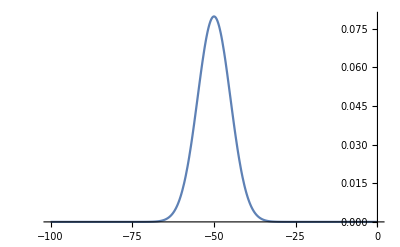

```mathematica
(*Agora, vamos proceder de forma diferente do notebook anterior e ploduzir o STS a partir do Cp de Schrodinger espacial relacionado a essa partícula, relembre que isso foi feito através da condição inicial do Muga:*)
Plot[muga[x],{x,-100,0} , PlotRange -> All]
```

```mathematica
NIntegrate[muga[x],{x,-100,0}](*vamos testar a normalização da condição inicial proposta pelo Muga apenas por desencargo de consciência*)
```

1.

```mathematica
Integrate[(1/Sqrt[2*Pi])*(1/(2*Pi*δ^2)^(1/4))*Exp[-((x-x0)^2/(4*δ^2))+(I*p0*x)/h]*Exp[-(I*(p*x))],{x,-∞,∞}](*Isto é, o Cp schrodinger dessa c.i. pode ser facilmente obtido através da transformada de fourier:*)
```

ConditionalExpression[((2/π)^(1/4) √(1/δ^2) (δ^2)^(3/4))/(ⅇ^(((h p-p0) (ⅈ h x0+(h p-p0) δ^2))/h^2)), Re[δ^2]>0]

```mathematica
cp [p_]:=((2/Pi)^(1/4)*Sqrt[1/5^2]*(5^2)^(3/4))/
   Exp[((1*p - 1)*(I*1*(-50) + (1*p - 1)*5^2))/1^2](*definindo uma função para chamar dentro da integração do STS*)
```

```mathematica
NIntegrate[Abs[cp[p]]^2,{p,0,10}](*Aqui é possível verificar a normalização do Cp*)
```

1.

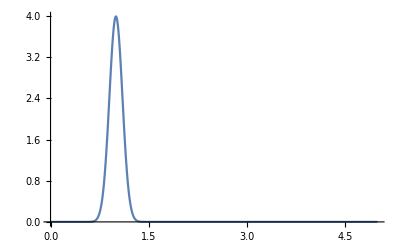

```mathematica
Plot[ Abs[cp[p]]^2, {p , 0 , 5}, PlotRange->All  , MaxRecursion->10]
```

```mathematica
(*Agora,adicionando o propagador e voltando a transformada de Fourier com o Cp calculado para schrodinger para obter uma nova distribuição temporal STS: *)sts[x_,t_]:=NIntegrate[(1/Sqrt[Pi])*Sqrt[p] *cp[p] *Exp[(I*(p*x))]*Exp[-(I*t*p^2)],{p,0,100}]
```

```mathematica
Abs[sts[0,2]]^2 (*Rodando pra um valor arbitrário antes de plotar só pra ver se ocorreu tudo bem com a integral em termos de convergencia etc*)
```

6.12493×10^-20

```mathematica
NIntegrate[Abs[sts[0,t]]^2, {t, 0, 60}] (*perceba que essa distribuição do sts já está normalizada como eduardo falou, "a noção de probabilidade vem daquela raíz de p, ela e o cp que transformam o sts num,a distribuição de probabilidade temporal da nossa particula"*)
```

1.

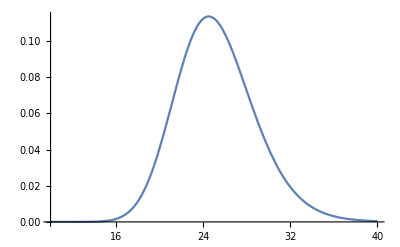

```mathematica
Plot[Abs[sts[0,t]]^2,{t,10,40},PlotRange->All, MaxRecursion->5] (*Plotando a curva sts para detector na posição x = 0, aparentemente com as correções o comportamento bate okay com o gráfico do muga!*)
```

```mathematica
(*para calcular o J tal qual fizemos em python*)
nmais[t_]:= NIntegrate[Abs[(E^((I*1*(0.5*(x+50)^2+2*1*t*(-50))-2*1*(1*t-2*0.5*x)*5^2)/(2*1*(1*t-2*I*0.5*5^2)))*(2*Pi)^(1/4)*(1*Sqrt[(I*1*t)/0.5+2*5^2]*Sqrt[(I*0.5*(1*(x+50)-2*I*1*5^2)^2)/(1^2*(1*t-2*I*0.5*5^2))]*Erf[Sqrt[(I*0.5*(1*x-1*(-50)-2*I*1*5^2)^2)/(1^2*(1*t-2*I*0.5*5^2))]/Sqrt[2]]+(1*(x+50)-2*I*1*5^2)*(-2*I+Erfi[(1*x-1*(-50)-2*I*1*5^2)/(1*Sqrt[(2*I*1*t)/0.5+4*5^2])])))/((5^2)^(1/4)*Sqrt[(2*I*1*t)/0.5+4*5^2]*((-I)*1*(x+50)-2*1*5^2))]^2,{x,0.001,0.999}]
```

```mathematica
dwelltime = NIntegrate[nmais[t],{t,0.001,0.999}]
```

2.25728×10^-23

```mathematica
j0[t_]:= dndtinterpol[t+0.62] + dwelltime
```

```mathematica
NSolve[A* NIntegrate[j0[t],{t,10,50}] == 1,A]
```

{{A→0.868721}}

```mathematica
stsinterpol=FunctionInterpolation[Abs[sts[0,t]]^2,{t,10,60}]//Quiet
```

InterpolatingFunction[…]

```mathematica
(*Vamos agora fazer o plot do STS e do modelo do muga sobrepostos comm o detector na posição x = 0, ambos os casos normalizados, para verificar a compatibilidade dos dois modelos*)
Plot[{Abs[sts[0,t]]^2,dndtnorm[t],0.8687207449837796*j0[t]},{t,10,40}, PlotLegends->Automatic]
```

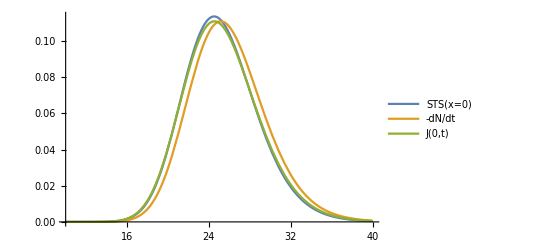

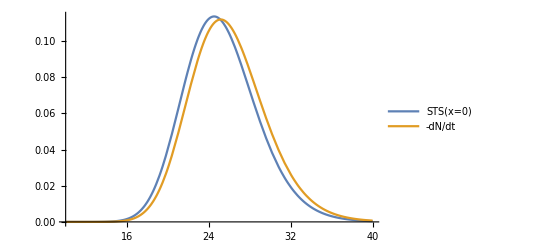

```mathematica
(*Agora, movendo o detector para a posição x = 10 e reavaliando os dois juntos novamente*)
dndtevolve[t_]:=NIntegrate[Abs[(E^((I*1*(0.5*(x+60)^2+2*1*t*(-60))-2*1*(1*t-2*0.5*x)*5^2)/(2*1*(1*t-2*I*0.5*5^2)))*(2*Pi)^(1/4)*(1*Sqrt[(I*1*t)/0.5+2*5^2]*Sqrt[(I*0.5*(1*(x+60)-2*I*1*5^2)^2)/(1^2*(1*t-2*I*0.5*5^2))]*Erf[Sqrt[(I*0.5*(1*x-1*(-60)-2*I*1*5^2)^2)/(1^2*(1*t-2*I*0.5*5^2))]/Sqrt[2]]+(1*(x+50)-2*I*1*5^2)*(-2*I+Erfi[(1*x-1*(-60)-2*I*1*5^2)/(1*Sqrt[(2*I*1*t)/0.5+4*5^2])])))/((5^2)^(1/4)*Sqrt[(2*I*1*t)/0.5+4*5^2]*((-I)*1*(x+60)-2*1*5^2))]^2*(2/(1*(x-1)*(x+(1/(1+I*1))))),{x,0.001,0.999}]
```

```mathematica
dn10=FunctionInterpolation[Re[-dndtevolve[t]],{t,10,70}]//Quiet
```

InterpolatingFunction[…]

```mathematica
NSolve[A*NIntegrate [dn10[t],{t,10,60}]==1,A]
```

{{A→1.17078}}

```mathematica
nmais10[t_]:= NIntegrate[Abs[(E^((I*1*(0.5*(x+60)^2+2*1*t*(-60))-2*1*(1*t-2*0.5*x)*5^2)/(2*1*(1*t-2*I*0.5*5^2)))*(2*Pi)^(1/4)*(1*Sqrt[(I*1*t)/0.5+2*5^2]*Sqrt[(I*0.5*(1*(x+60)-2*I*1*5^2)^2)/(1^2*(1*t-2*I*0.5*5^2))]*Erf[Sqrt[(I*0.5*(1*x-1*(-60)-2*I*1*5^2)^2)/(1^2*(1*t-2*I*0.5*5^2))]/Sqrt[2]]+(1*(x+50)-2*I*1*5^2)*(-2*I+Erfi[(1*x-1*(-60)-2*I*1*5^2)/(1*Sqrt[(2*I*1*t)/0.5+4*5^2])])))/((5^2)^(1/4)*Sqrt[(2*I*1*t)/0.5+4*5^2]*((-I)*1*(x+60)-2*1*5^2))]^2,{x,0,1}]
```

```mathematica
dwelltime = NIntegrate[nmais10[t],{t,0,1}]
```

8.0661×10^-29

```mathematica
j10[t_]:= dn10[t+0.62] + dwelltime
```

```mathematica
NSolve[A* NIntegrate[j10[t],{t,10,50}] == 1,A]
```

{{A→1.17109}}

```mathematica
Plot[{Abs[sts[10,t]]^2,dn10[t]*1.1797830756759672, 1.1710944640735108*j10[t]},{t,15,50}, PlotLegends->Automatic]
```

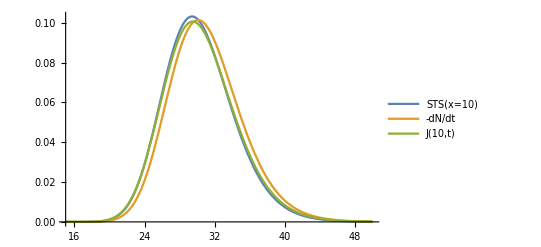

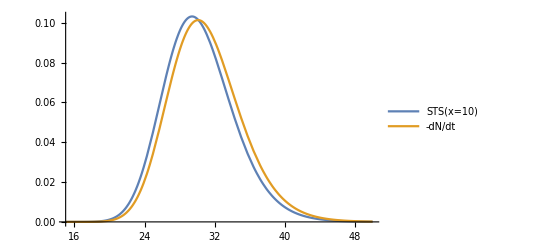

```mathematica
(*Atendendo a pedidos antigos de eduardo, fazendo mais uma vez o gráfico agora para x=20*)
dndtevolve2[t_]:=NIntegrate[Abs[(E^((I*1*(0.5*(x+70)^2+2*1*t*(-70))-2*1*(1*t-2*0.5*x)*5^2)/(2*1*(1*t-2*I*0.5*5^2)))*(2*Pi)^(1/4)*(1*Sqrt[(I*1*t)/0.5+2*5^2]*Sqrt[(I*0.5*(1*(x+70)-2*I*1*5^2)^2)/(1^2*(1*t-2*I*0.5*5^2))]*Erf[Sqrt[(I*0.5*(1*x-1*(-70)-2*I*1*5^2)^2)/(1^2*(1*t-2*I*0.5*5^2))]/Sqrt[2]]+(1*(x+70)-2*I*1*5^2)*(-2*I+Erfi[(1*x-1*(-70)-2*I*1*5^2)/(1*Sqrt[(2*I*1*t)/0.5+4*5^2])])))/((5^2)^(1/4)*Sqrt[(2*I*1*t)/0.5+4*5^2]*((-I)*1*(x+70)-2*1*5^2))]^2*(2/(1*(x-1)*(x+(1/(1+I*1))))),{x,0.001,0.999}]
```

```mathematica
dn20=FunctionInterpolation[Re[-dndtevolve2[t]],{t,15,75}]//Quiet
```

InterpolatingFunction[…]

```mathematica
NSolve[A*NIntegrate [dn20[t],{t,15,70}]==1,A]
```

{{A→0.868717}}

```mathematica
nmais20[t_]:= NIntegrate[Abs[(E^((I*1*(0.5*(x+70)^2+2*1*t*(-70))-2*1*(1*t-2*0.5*x)*5^2)/(2*1*(1*t-2*I*0.5*5^2)))*(2*Pi)^(1/4)*(1*Sqrt[(I*1*t)/0.5+2*5^2]*Sqrt[(I*0.5*(1*(x+70)-2*I*1*5^2)^2)/(1^2*(1*t-2*I*0.5*5^2))]*Erf[Sqrt[(I*0.5*(1*x-1*(-70)-2*I*1*5^2)^2)/(1^2*(1*t-2*I*0.5*5^2))]/Sqrt[2]]+(1*(x+70)-2*I*1*5^2)*(-2*I+Erfi[(1*x-1*(-70)-2*I*1*5^2)/(1*Sqrt[(2*I*1*t)/0.5+4*5^2])])))/((5^2)^(1/4)*Sqrt[(2*I*1*t)/0.5+4*5^2]*((-I)*1*(x+70)-2*1*5^2))]^2,{x,0,1}]
```

```mathematica
dwelltime = NIntegrate[nmais20[t],{t,0,1}]
```

```mathematica
j20[t_]:= dn20[t+0.62] + dwelltime
```

```mathematica
NSolve[A* NIntegrate[j20[t],{t,10,50}] == 1,A]
```

{{A→0.872916}}

```mathematica
Plot[{Abs[sts[20,t]]^2,dn20[t]*0.8787169119170634, 0.872916100664042*j20[t]},{t,20,55}, PlotLegends->Automatic]
```